```mathematica
Clear[θr]
γ:= 1.7595*10^11;
α:= 0.1;
Subscript[H, app]:= {0,0,0};
LL1[H_]:=-γ/(1+α^2)(Cross[m1[t],H]+ α*Cross[m1[t],Cross[m1[t],H]]);
LL2[H_]:=-γ/(1+α^2)(Cross[m2[t],H]+ α*Cross[m2[t],Cross[m2[t],H]]);
H[r_,θ_,θoff_,ϕ_,x1_,y1_,m2_]:=(4π*10^-7*3*(10^-19))/(4π(r)^5)*((m2[[1]])*(x1 Cos[θoff/2]-y1 Cos[θ-θoff/2])*Cos[ϕ]+(m2[[2]])*(x1 Cos[θoff/2]-y1 Cos[θ-θoff/2])*Sin[ϕ]+(m2[[3]])*(x1 Sin [θoff/2]-y1 Sin[θ- θoff/2]))*{((x1 Cos[θoff/2]-y1 Cos[θ- θoff/2])* Cos [ϕ]-((m2[[1]])*r^2/3)),((x1 Cos[θoff/2]-y1 Cos[θ- θoff/2])*Sin [ϕ]-((m2[[2]])*r^2/3)),(x1 Sin [θoff/2]-y1 Sin[θ-θoff/2]-(m2[[3]])*r^2/3)};

ro[x1_,y1_,θ_,θoff_]:=√(x1^2+y1^2-2x1 y1 Cos[θ-θoff]);
θr[θ_]:=θ*π/180;
Happ:={0,0,0.01};
H[ro[28.7045*10^-9,28.7045*10^-9,θr[HingeAngles[[232]][[1]]],0.237172],θr[HingeAngles[[232]][[1]]],0.237172,π/2,28.7045*10^-9,28.7045*10^-9,{0,0,1}]
Hf1:=RandomVariate[NormalDistribution[],3];
Subscript[H, th,mag]= ((2*1.38*10^-23*300*α)/(γ*10^-19*10^-12))^(1/2);
Clear[list]
list=Hf1
Subscript[H, th,norm]:= Subscript[H, th,mag]/(√(list[[1]]^2+list[[2]]^2+list[[3]]^2))list
Subscript[H, sp][m_]:=((2*10000)/(10^-19/(4/3 π(2.5*10^-9)^3))m.{0,0.02,0.98}){0,0.02,0.98};

HingeAngles=Import["E:\\physics stuff\\JH research\\Calculations\\Calculations\\HingeAngles.csv"];
HingeAngles[[2]][[1]]
```

{0.,-0.00455499,0.0127534}

{0.775924,-0.760485,0.485847}

0.17017

If there is an error saying Hinge Angles longer than depth of object, then execute the hinge angles import

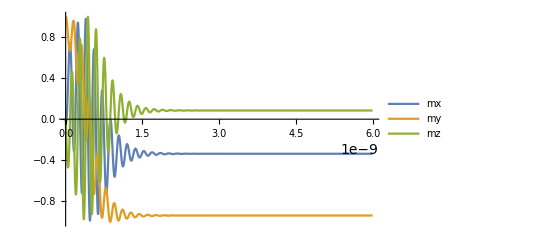

```mathematica
sols=NDSolve[{m1'[t]==LL1[Subscript[H, th,norm]+Subscript[H, sp][m1[t]]+H[ro[18.322*10^-9,18.322*10^-9,θr[HingeAngles[[232]][[1]]],0.369074],θr[HingeAngles[[232]][[1]]],0.369074,π/2,18.322*10^-9,18.322*10^-9,{0,0,1}]],m1[0]=={0,1,0}},m1,{t,0,10^-7},MaxSteps->∞];
Plot[{Evaluate[m1[t]/.sols][[1]][[1]],Evaluate[m1[t]/.sols][[1]][[2]], Evaluate[m1[t]/.sols][[1]][[3]]},{t,0,6*10^-9}, PlotLegends->{"mx","my","mz"}]
```

```mathematica
"FOR ALL ANGLES"
finalm1={};
finalm2={};
For[i=1, i≤10, i=i+1,{{
testcase2=Module[{a=0,t0=0,tf=5*10^(-9),dt=10^(-11),m1val={0,1,0},m2val={0,0,1}},{{Hf2:=RandomVariate[NormalDistribution[],3];
Clear[list1],
list1=Hf2,
Subscript[H, th,norm]:= Subscript[H, th,mag]/(√(list1[[1]]^2+list1[[2]]^2+list1[[3]]^2))list1},Table[If[EvenQ[a],sol1=NDSolve[{m1'[t]==LL1[Subscript[H,sp][m1[t]]+Subscript[H, th,norm]+H[ro[28.7045*10^-9,28.7045*10^-9,θr[HingeAngles[[i]][[1]]],0.237172],θr[HingeAngles[[i]][[1]]],0.237172,π/2,28.7045*10^-9,28.7045*10^-9,m2val]],m1[j]==m1val},m1,{t,j,j+dt},MaxSteps->∞];
Evaluate[m1[t]/.sol1][[1]];
m1val=Evaluate[m1[t]/.sol1][[1]]/.{t->j+dt};
a++;
{sol1,m1val},sol2=NDSolve[{m2'[t]==LL2[Subscript[H,sp][m2[t]]+Subscript[H, th,norm]+H[ro[28.7045*10^-9,28.7045*10^-9,θr[HingeAngles[[i]][[1]]],0.237172],θr[HingeAngles[[i]][[1]]],0.237172,π/2,28.7045*10^-9,28.7045*10^-9,m1val]],m2[j]==m2val},m2,{t,j,j+dt},MaxSteps->∞];
Evaluate[m2[t]/.sol2][[1]];
m2val=Evaluate[m2[t]/.sol2][[1]]/.{t->j+dt};
a++;
{sol2,m2val}],{j,t0,tf,dt}]}],{AppendTo[finalm1, testcase2[[2]][[501]][[2]]]},{AppendTo[finalm2, testcase2[[2]][[500]][[2]]]}}}
]
```

FOR ALL ANGLES

2 LISTS ARE CREATED TO STORE THE VALUES OF ‘m1’ AND ‘m2’ AT A TIME WHEN BOTH OF THEM ARE FAIRLY CONSTANT (5ns IN THIS CASE), FOR ALL ANGLES

2 LISTS ARE CREATED TO STORE THE MAGNETIC FEILDS OF THE 2 SPIONS AT THE VALUES FOR ‘m1’ AND ‘m2’ FROM THE ABOVE LISTS

```mathematica
H1list={};
H2list={};
```

```mathematica
For[i=1,i≤10,i=i+1,{{H1=H[ro[28.7045*10^-9,28.7045*10^-9,θr[HingeAngles[[i]][[1]]],0.237172],θr[HingeAngles[[i]][[1]]],0.237172,π/2,28.7045*10^-9,28.7045*10^-9,finalm1[[i]]]},{AppendTo[H1list,H1]}}]
```

```mathematica
For[i=1,i≤10,i=i+1,{{H2=H[ro[28.7045*10^-9,28.7045*10^-9,θr[HingeAngles[[i]][[1]]],0.237172],θr[HingeAngles[[i]][[1]]],0.237172,π/2,28.7045*10^-9,28.7045*10^-9,finalm2[[i]]]},{AppendTo[H2list,H2]}}]
```

```mathematica
H1list
```

{{8.31248×10^-11,-4.49947×10^-12,0.0406007},{6.03233×10^-11,-0.0000489745,0.0329791},{1.05151×10^-10,-0.000192551,0.0648312},{1.67347×10^-11,0.000473507,-0.106285},{1.13216×10^-10,0.000528624,-0.0889921},{7.63254×10^-12,-0.0000276658,0.00372593},{-2.69582×10^-11,-0.000136447,0.0153134},{1.67873×10^-11,-0.00130631,0.125661},{3.35788×10^-11,-0.00138506,0.116581},{-5.58266×10^-11,0.00144281,-0.107947}}

ENERGY =  - m . H (only m2)

```mathematica
Energy={};

For[i=1,i≤10,i=i+1,{{E1=Dot[H1list[[i]],finalm2[[i]]]},{E2=Dot[H2list[[i]],finalm1[[i]]]},{AppendTo[Energy,(E1)*(-10^(-19))/(300*1.38*10^(-23))]}}]
```

```mathematica
Energy
```

{-0.415827,-0.264244,-0.982979,-2.54185,-1.71367,-0.00290027,-0.0467775,-3.02897,-2.50165,-2.05694}

The iteration for calculating energy is run for all angles in the excel file, but the calculation for the impossible angles (any angle before 250th angle) is redundant therefore the below graph skips those points

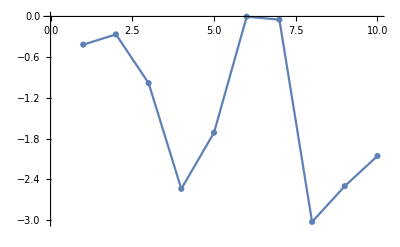

```mathematica
EmagGraph=ListLinePlot[Energy,PlotMarkers->{Automatic},PlotRange->Automatic]
```